### Chapter XII Styling and customizing graphics

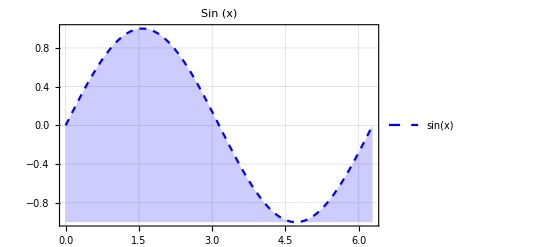

```mathematica
Plot[Sin[x],{x,0,2π},PlotTheme->"Detailed",PlotStyle->{Blue,Dashed,Thick},Filling->Bottom,PlotLabel->"Sin (x)"]
```

By Graph-> Drawing tools, one can interact with the graphic intuitively

Finding Options

```mathematica
Take[Options[Plot]]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

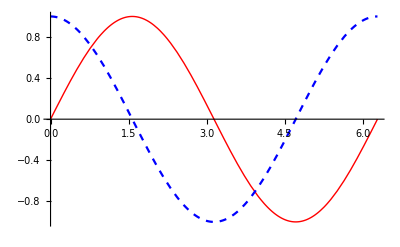

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 π},PlotStyle->{Directive[Red,Thick],Directive[Blue,Dashed]}]
```

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->ColorData["Rainbow"],Mesh->None]
```

-Graphics3D-

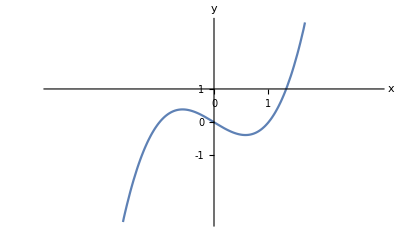

```mathematica
Plot[x^3-x,{x,-3,3},PlotRange->{-3,3},AxesOrigin->{0,1},Ticks->{{0,1},{-1,0,1}},AxesLabel->{"x","y"},PlotLegends->Placed["First curve",Top]]
```

```mathematica
Plot[{Callout[Sin[x],"sin(x)",Top],Callout[Cos[x],"cos(x)",Bottom]},{x,0,2 π},PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed]}]
```

-Graphics-

```mathematica
Plot[Callout[Tan[x],"tan(x)",π],{x,0,2 π},Epilog->{PointSize[Large],Point[{π,0}]}]
```

-Graphics-

```mathematica
ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2 π},{v,-π,π},PlotStyle->Opacity[0.3],Mesh->None]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5 ϕ] Sin[10 θ]/10,{θ,0,π},{ϕ,0,2 π},Boxed->False,Background->LightBlue,Lighting->"ThreePoint",PlotStyle->{Texture[-Graphics-]}]
```

-Graphics3D-

```mathematica
ExampleData[{"Texture","Grass3"}]
```

-Graphics-

```mathematica
mySettings=PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed]};
```

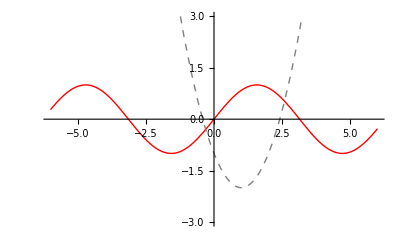

```mathematica
Plot[{Sin[x],x^2-2 x-1},{x,-6,6},PlotRange->3,Evaluate[mySettings]]
```

```mathematica
myPlot[eq1_,eq2_]:=Plot[{eq1,eq2},{x,0,2 π},PlotStyle->{Directive[Red,Thick],Directive[Gray,Thick,Dashed]},PlotLegends->Placed["Expressions",Above]]
```

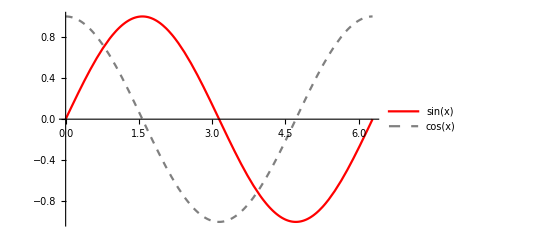

```mathematica
myPlot[Sin[x],Cos[x]]
```